## Determining Repeatability of the project

```mathematica
IntraclassCorrelation[data_]:=Variance[Mean[#]&/@data]/(Variance[Mean[#]&/@data]+Mean[Variance[#]&/@data])//N
```

### Import Data and filter just the ones actually in the data set

```mathematica
rawIDs=Import["/Users/katjad/Documents/Github/SheepCapstone/ids.csv","Numeric"->False];
```

```mathematica
eartagsToFID=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/IDmatching/eartagsToFID.mx"];
```

```mathematica
indexToEartag=AssociationThread[Range[51],rawIDs[[2;;,2]]];
```

```mathematica
indexToFID=indexToEartag/.eartagsToFID;
```

```mathematica
indexToFIDNoNA = DeleteCases[indexToFID,"NA"];
```

```mathematica
FIDICC = IntraclassCorrelation[Values[indexToFIDNoNA]]
```

0.615479

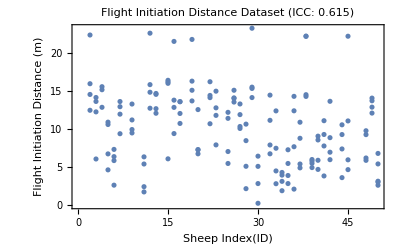

```mathematica
ListPlot[Catenate[DeleteCases[MapIndexed[{#2[[1]],#1}&,Values[indexToFID],{2}],"NA"]],Frame->True,FrameLabel->{"Sheep Index(ID)","Flight Initiation Distance (m)"},PlotLabel->"Flight Initiation Distance Dataset (ICC: 0.615)"]
```

### Repeat for the Exploration Tendency

```mathematica
explorationRaw=Import["/Users/katjad/Documents/Github/SheepCapstone/buckets.csv","Numeric"->False];
```

```mathematica
flagToET=#[[2]]->Ceiling[Length[DeleteCases[#[[9;;71-LengthWhile[Reverse[#],Function[x,x==="NA"]]]],"NA"]]/3]&/@explorationRaw[[2;;]];
```

Part::take: Cannot take positions 9 through 7 in {29,199,1,1,2018-03-09,NA,Started 10 sec before vid starts,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,«21»}.

```mathematica
eartagToFlags= ToString/@Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/IDmatching/earflags.mx"];
```

```mathematica
indexToEartag=AssociationThread[Range[51],rawIDs[[2;;,2]]];
```

```mathematica
flagtoET=KeySort[Merge[flagToET,#&]];
```

```mathematica
indexToFlag=indexToEartag/.eartagToFlags;
```

```mathematica
indexToET=indexToFlag/.flagtoET;
```

```mathematica
ETICC = IntraclassCorrelation[Values[DeleteCases[indexToET,"NA"]]]
```

0.404685

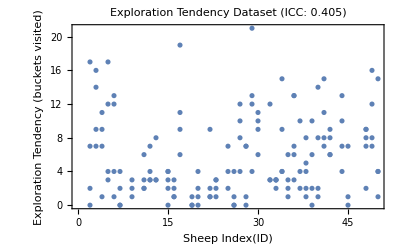

```mathematica
ListPlot[Catenate[DeleteCases[MapIndexed[{#2[[1]],#1}&,Values[indexToET],{2}],"NA"]],Frame->True,FrameLabel->{"Sheep Index(ID)","Exploration Tendency (buckets visited)"},PlotLabel->"Exploration Tendency Dataset (ICC: 0.405)"]
```

## Export for use in R

```mathematica
indexAndFID=Catenate[DeleteCases[MapIndexed[{#2[[1]],#1}&,Values[indexToFID],{2}],"NA"]];
```

```mathematica
Export["/Users/katjad/Documents/Github/SheepCapstone/indexAndFID.csv",indexAndFID,"CSV"];
```

```mathematica
indexAndET = Catenate[DeleteCases[MapIndexed[{#2[[1]],#1}&,Values[indexToET],{2}],"NA"]];
Export["/Users/katjad/Documents/Github/SheepCapstone/indexAndET.csv",indexAndET,"CSV"]
```

/Users/katjad/Documents/Github/SheepCapstone/indexAndET.csv